```mathematica
SetDirectory["/Volumes/MicroSD/2_PostDoc_SD/phonons_vo2/post_proc_r_tet/b"]
vo2Data=ReadList["allBands.out",Table[Number,{i,1,23}]];
```

/Volumes/MicroSD/2_PostDoc_SD/phonons_vo2/post_proc_r_tet/b

```mathematica
vo2Data[[2]]
```

{2,0.,0.,0.495,-6.11431,-6.00117,4.72892,4.72892,6.92869,6.92869,7.48571,7.48571,8.53139,8.68031,12.3503,12.4457,13.0892,13.0892,15.2331,15.2331,18.3108,0.0333687,0.99}

```mathematica
originalBandi[i_]:=Transpose@{Transpose[vo2Data][[1]],Transpose[vo2Data][[4+i]]}
```

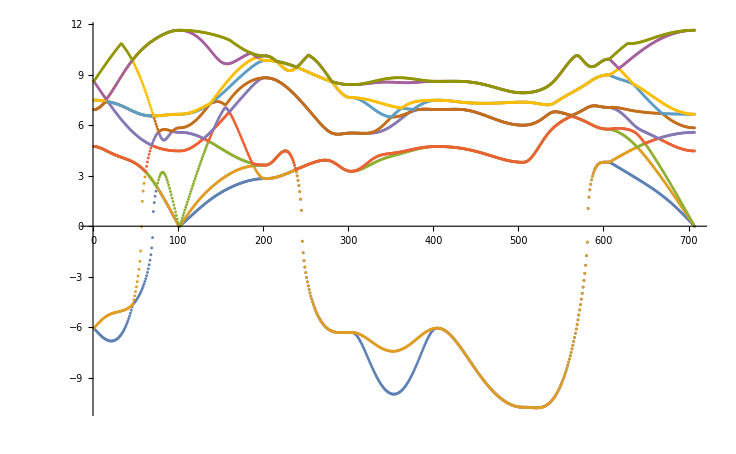

```mathematica
ListPlot@Table[originalBandi[i],{i,1,10}]
```

```mathematica
tFunction[arg_,beta_,mu_]:=1/(Exp[-beta*(arg/0.5-mu)]+1)
tFunctionLin[arg_,beta_,mu_]:=arg/0.5
```

```mathematica
(*4 is qfrac, 6 was tempfrac, whhici is just*)
```

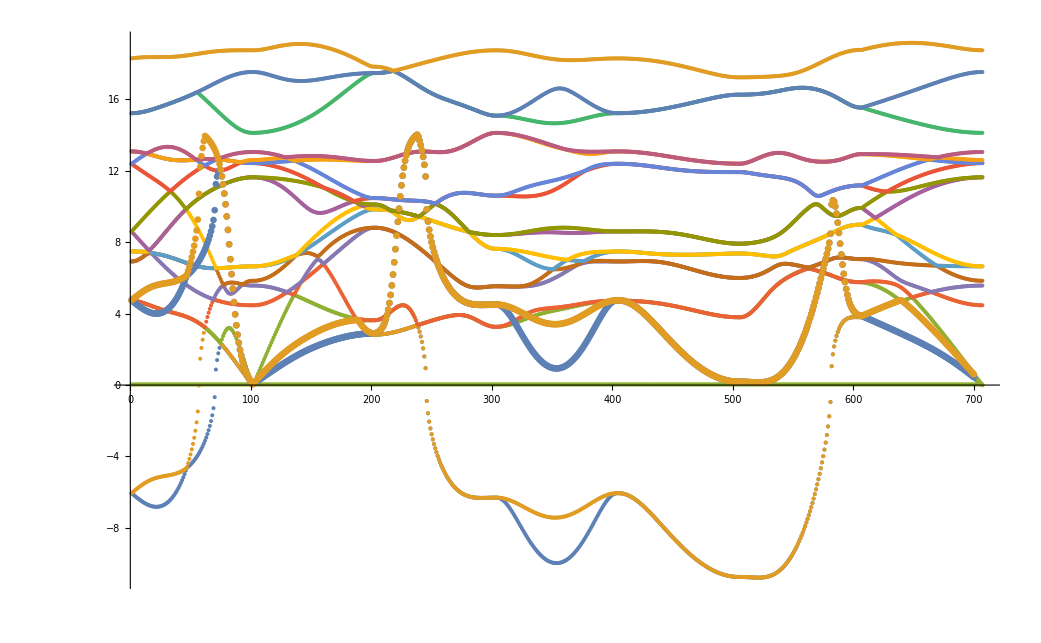

```mathematica
With[{mu=0.01*18,beta=28},transformedBandA=Table[{Transpose[vo2Data][[1]][[i]],Transpose[vo2Data][[5]][[i]]+tFunction[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[vo2Data][[5]][[i]]^2)^0.5},{i,1,700}];
transformedBandB=Table[{Transpose[vo2Data][[1]][[i]],Transpose[vo2Data][[6]][[i]]+tFunction[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[vo2Data][[6]][[i]]^2)^0.5},{i,1,700}];
Show[{ListPlot@Table[originalBandi[i],{i,1,18}],ListPlot[{transformedBandA,transformedBandB},Frame->True,ImageSize->600,FrameLabel->{"q-index","energy"},PlotLabel->{Text@StringJoin@{"Mu=",ToString@mu},Text@StringJoin@{"Beta=",ToString@beta}
}]},PlotRange->All]]
```

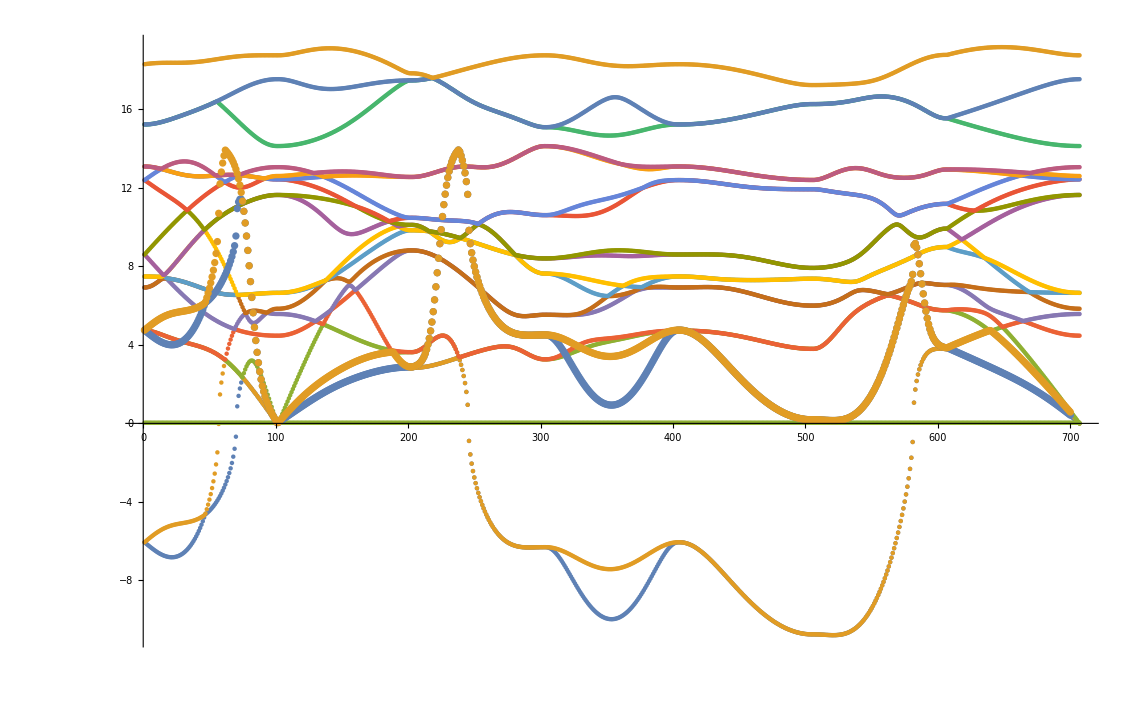

```mathematica
With[{mu=0.01*20,beta=27,Tc=341,
T0=329.65,
omega0R=-10.7507508144},Tfrac=(Tc-T0)/T0;transformedBandA=Table[{Transpose[vo2Data][[1]][[i]],Transpose[vo2Data][[5]][[i]]+tFunction[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[vo2Data][[5]][[i]]^2)^0.5},{i,1,700}];
transformedBandB=Table[{Transpose[vo2Data][[1]][[i]],Transpose[vo2Data][[6]][[i]]+tFunction[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[vo2Data][[6]][[i]]^2)^0.5},{i,1,700}];
Show[{ListPlot@Table[originalBandi[i],{i,1,18}],ListPlot[{transformedBandA,transformedBandB},Frame->True,ImageSize->600,FrameLabel->{"q-index","energy"},PlotLabel->{Text@StringJoin@{"Mu=",ToString@mu},Text@StringJoin@{"Beta=",ToString@beta}
}]},PlotRange->All]]
```

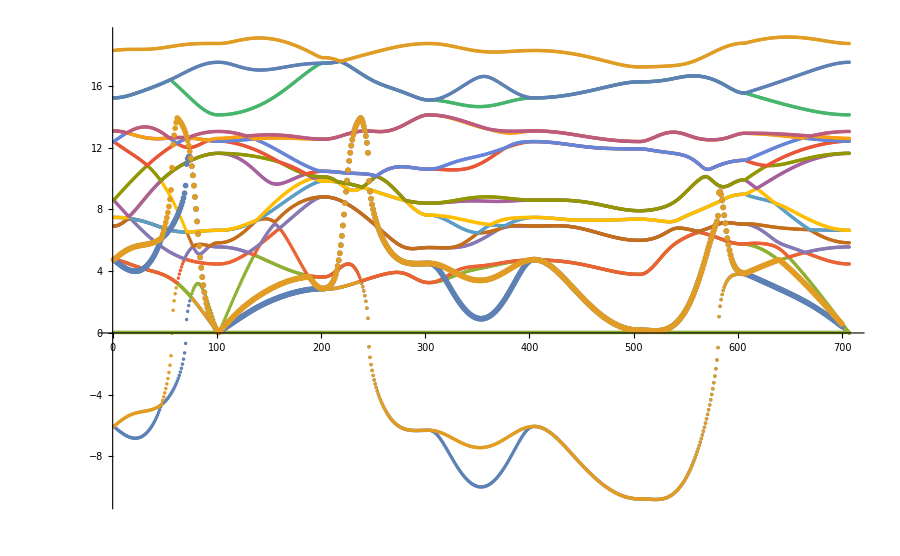

```mathematica
With[{mu=0.01*20,beta=27,Tc=340.65,
T0=329.65,
Tfrac=(Tc-T0)/Tc,
omega0R=-10.7507508144},transformedBandA=Table[{Transpose[vo2Data][[1]][[i]],Transpose[vo2Data][[5]][[i]]+tFunction[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[vo2Data][[5]][[i]]^2)^0.5},{i,1,700}];
transformedBandB=Table[{Transpose[vo2Data][[1]][[i]],Transpose[vo2Data][[6]][[i]]+tFunction[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[vo2Data][[6]][[i]]^2)^0.5},{i,1,700}];
Show[{ListPlot@Table[originalBandi[i],{i,1,18}],ListPlot[{transformedBandA,transformedBandB},Frame->True,ImageSize->600,FrameLabel->{"q-index","energy"},PlotLabel->{Text@StringJoin@{"Mu=",ToString@mu},Text@StringJoin@{"Beta=",ToString@beta}
}]},PlotRange->All,ImageSize->900]]
```

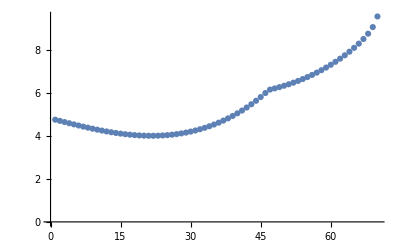

```mathematica
ListPlot@With[{mu=0.01*20,beta=27},Join[Table[{Transpose[vo2Data][[1]][[i]],Transpose[vo2Data][[5]][[i]]+tFunction[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[vo2Data][[5]][[i]]^2)^0.5},{i,1,70}]]]
```

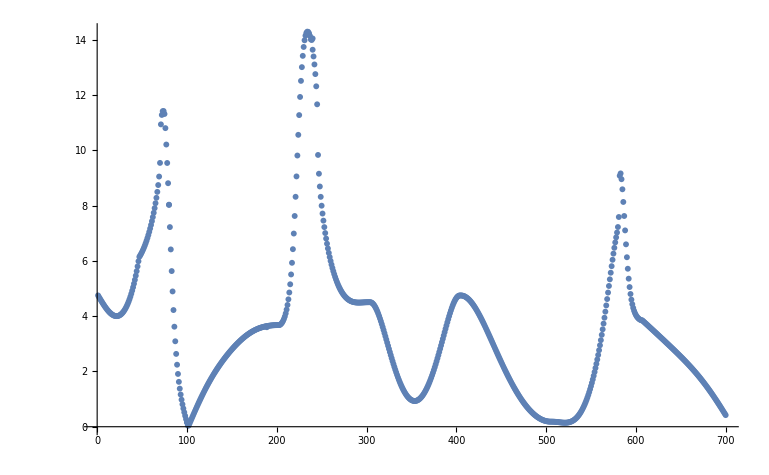

```mathematica
ListPlot[With[{mu=0.01*20,beta=27,p1=5,p2=6,p3=7,p4=5},Join[Table[{Transpose[vo2Data][[1]][[i]],Transpose[vo2Data][[p1]][[i]]+tFunction[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[vo2Data][[p1]][[i]]^2)^0.5},{i,1,80}],Table[{Transpose[vo2Data][[1]][[i]],Transpose[vo2Data][[p2]][[i]]+tFunction[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[vo2Data][[p2]][[i]]^2)^0.5},{i,80,100}],Table[{Transpose[vo2Data][[1]][[i]],Transpose[vo2Data][[p2]][[i]]+tFunction[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[vo2Data][[p2]][[i]]^2)^0.5},{i,100,189}],Table[{Transpose[vo2Data][[1]][[i]],Transpose[vo2Data][[p3]][[i]]+tFunction[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[vo2Data][[p3]][[i]]^2)^0.5},{i,189,240}],Table[{Transpose[vo2Data][[1]][[i]],Transpose[vo2Data][[p4]][[i]]+tFunction[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[vo2Data][[p4]][[i]]^2)^0.5},{i,240,700}]]],PlotRange->All]
```

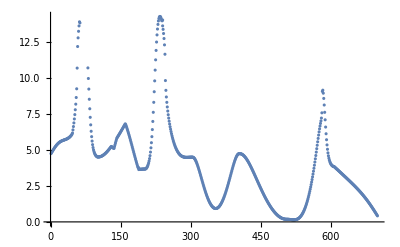

```mathematica
ListPlot[With[{mu=0.01*20,beta=27,p1=6,p2=8,p3=7,p4=5},Join[Table[{Transpose[vo2Data][[1]][[i]],Transpose[vo2Data][[p1]][[i]]+tFunction[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[vo2Data][[p1]][[i]]^2)^0.5},{i,1,63}],Table[{Transpose[vo2Data][[1]][[i]],Transpose[vo2Data][[p2]][[i]]+tFunction[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[vo2Data][[p2]][[i]]^2)^0.5},{i,80,100}],Table[{Transpose[vo2Data][[1]][[i]],Transpose[vo2Data][[p2]][[i]]+tFunction[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[vo2Data][[p2]][[i]]^2)^0.5},{i,100,189}],Table[{Transpose[vo2Data][[1]][[i]],Transpose[vo2Data][[p3]][[i]]+tFunction[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[vo2Data][[p3]][[i]]^2)^0.5},{i,189,240}],Table[{Transpose[vo2Data][[1]][[i]],Transpose[vo2Data][[p4]][[i]]+tFunction[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[vo2Data][[p4]][[i]]^2)^0.5},{i,240,700}]]],PlotRange->All]
```

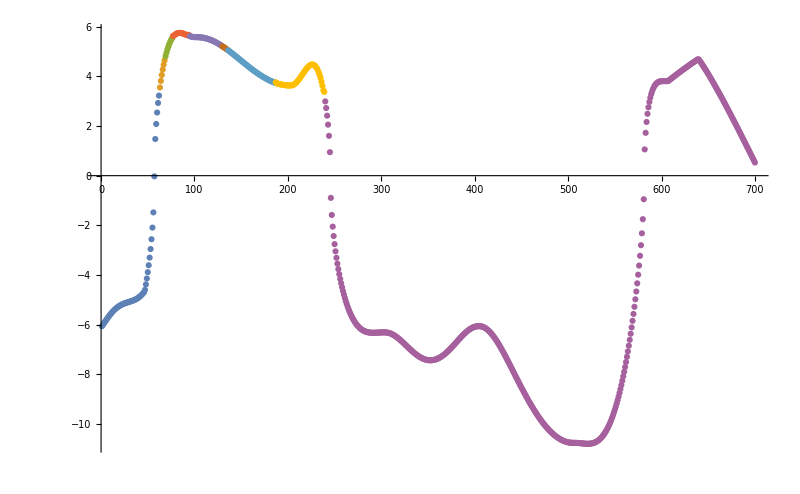

```mathematica
l1={originalBandi[1][[1;;75]],originalBandi[3][[76;;100]],originalBandi[2][[101;;188]],originalBandi[3][[189;;238]],originalBandi[1][[239;;700]]};
l2={originalBandi[2][[1;;62]],originalBandi[4][[63;;68]],originalBandi[5][[69;;76]],originalBandi[6][[77;;94]],originalBandi[5][[95;;129]],originalBandi[4][[130;;135]],originalBandi[3][[136;;186]],originalBandi[4][[187;;239]],originalBandi[2][[240;;700]]};
ListPlot[l2,ImageSize->800,PlotRange->All]
ListPlot[Join[l1,l2],ImageSize->800,PlotRange->All];
```

```mathematica
Join@@l1//Length
Join@@l2//Length
```

700

700

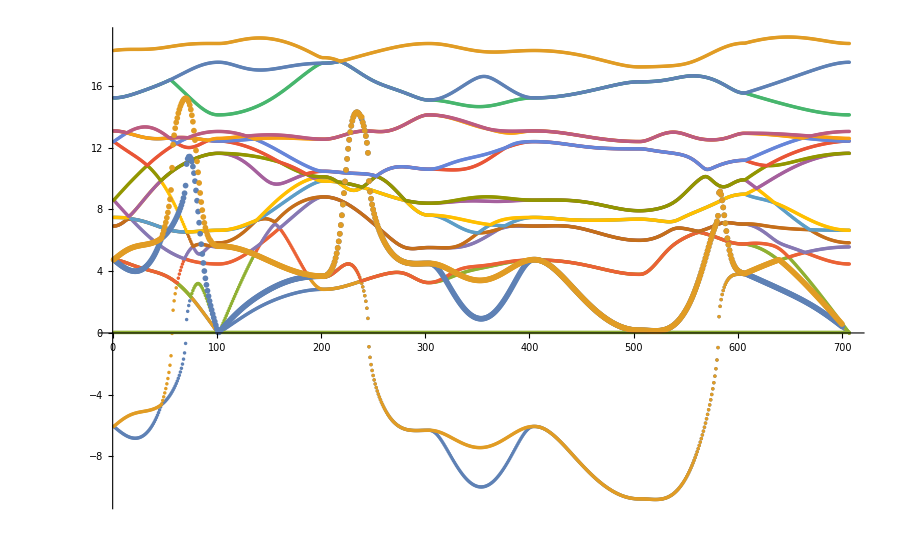

```mathematica
With[{mu=0.01*20,beta=27,Tc=340.65,
T0=329.65,
Tfrac=(Tc-T0)/Tc,
omega0R=-10.7507508144},transformedBandA=Table[{Transpose[Join@@l1][[1]][[i]],Transpose[Join@@l1][[2]][[i]]+tFunction[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[Join@@l1][[2]][[i]]^2)^0.5},{i,1,700}];
transformedBandB=Table[{Transpose[Join@@l2][[1]][[i]],Transpose[Join@@l2][[2]][[i]]+tFunction[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[Join@@l2][[2]][[i]]^2)^0.5},{i,1,700}];
Show[{ListPlot@Table[originalBandi[i],{i,1,18}],ListPlot[{transformedBandA,transformedBandB},Frame->True,ImageSize->600,FrameLabel->{"q-index","energy"},PlotLabel->{Text@StringJoin@{"Mu=",ToString@mu},Text@StringJoin@{"Beta=",ToString@beta}
}]},PlotRange->All,ImageSize->900]]
```

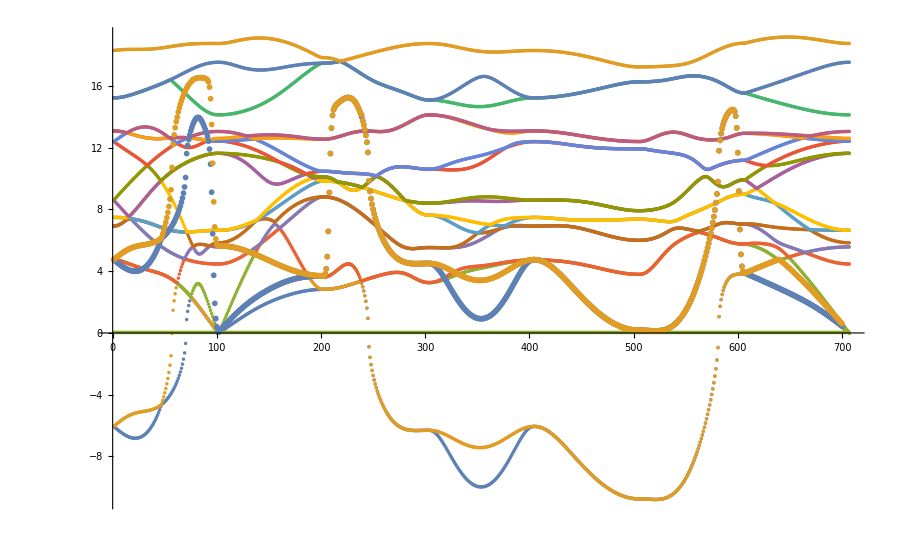

```mathematica
With[{mu=0.01*5,beta=100,Tc=340.65,
T0=329.65,
Tfrac=(Tc-T0)/Tc,
omega0R=-10.7507508144},transformedBandA=Table[{Transpose[Join@@l1][[1]][[i]],Transpose[Join@@l1][[2]][[i]]+tFunction[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[Join@@l1][[2]][[i]]^2)^0.5},{i,1,700}];
transformedBandB=Table[{Transpose[Join@@l2][[1]][[i]],Transpose[Join@@l2][[2]][[i]]+tFunction[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[Join@@l2][[2]][[i]]^2)^0.5},{i,1,700}];
Show[{ListPlot@Table[originalBandi[i],{i,1,18}],ListPlot[{transformedBandA,transformedBandB},Frame->True,ImageSize->600,FrameLabel->{"q-index","energy"},PlotLabel->{Text@StringJoin@{"Mu=",ToString@mu},Text@StringJoin@{"Beta=",ToString@beta}
}]},PlotRange->All,ImageSize->900]]
```

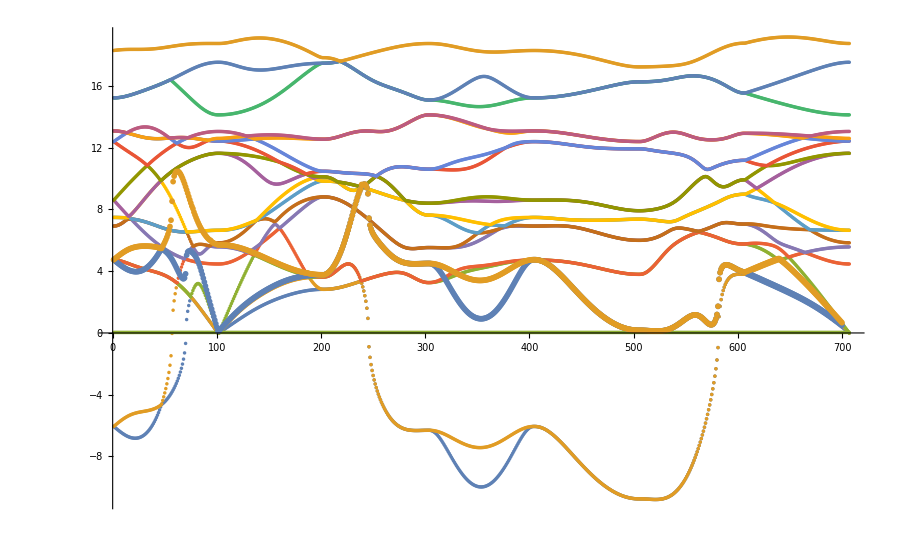

```mathematica
With[{mu=0.01*33.5,beta=13,Tc=340.65,
T0=329.65,
Tfrac=(Tc-T0)/Tc,
omega0R=-10.7507508144},transformedBandA=Table[{Transpose[Join@@l1][[1]][[i]],Transpose[Join@@l1][[2]][[i]]+tFunction[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[Join@@l1][[2]][[i]]^2)^0.5},{i,1,700}];
transformedBandB=Table[{Transpose[Join@@l2][[1]][[i]],Transpose[Join@@l2][[2]][[i]]+tFunction[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[Join@@l2][[2]][[i]]^2)^0.5},{i,1,700}];
Show[{ListPlot@Table[originalBandi[i],{i,1,18}],ListPlot[{transformedBandA,transformedBandB},Frame->True,ImageSize->600,FrameLabel->{"q-index","energy"},PlotLabel->{Text@StringJoin@{"Mu=",ToString@mu},Text@StringJoin@{"Beta=",ToString@beta}
}]},PlotRange->All,ImageSize->900]]
```

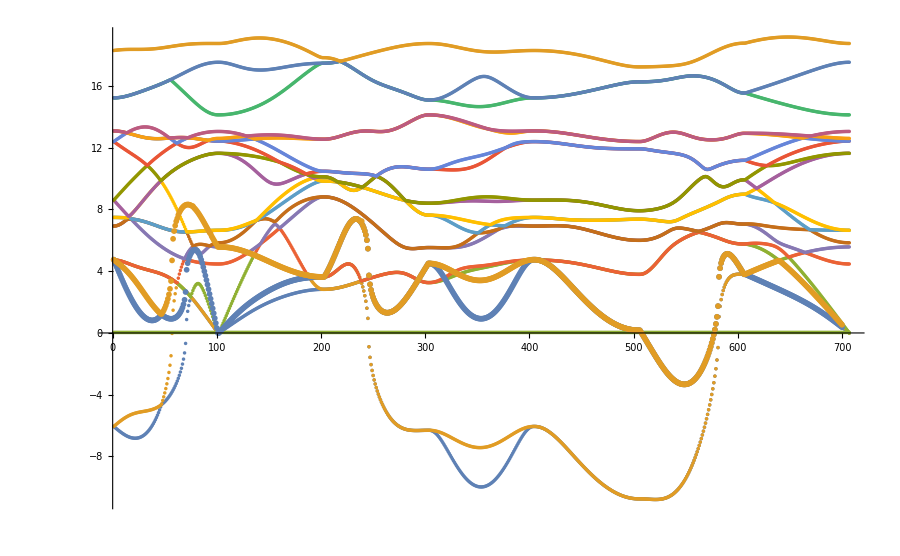

```mathematica
With[{mu=0.01*33.8,beta=13,Tc=340.65,
T0=329.65,
Tfrac=(Tc-T0)/Tc,
omega0R=-10.7507508144},transformedBandA=Table[{Transpose[Join@@l1][[1]][[i]],Transpose[Join@@l1][[2]][[i]]+tFunctionLin[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[Join@@l1][[2]][[i]]^2)^0.5},{i,1,700}];
transformedBandB=Table[{Transpose[Join@@l2][[1]][[i]],Transpose[Join@@l2][[2]][[i]]+tFunctionLin[Transpose[vo2Data][[4]][[i]],beta,mu]*(omega0R^2+Tfrac*Transpose[Join@@l2][[2]][[i]]^2)^0.5},{i,1,700}];
Show[{ListPlot@Table[originalBandi[i],{i,1,18}],ListPlot[{transformedBandA,transformedBandB},Frame->True,ImageSize->600,FrameLabel->{"q-index","energy"},PlotLabel->{Text@StringJoin@{"Mu=",ToString@mu},Text@StringJoin@{"Beta=",ToString@beta}
}]},PlotRange->All,ImageSize->900]]
```

```mathematica
11
```

```mathematica
Transpose[Table[originalBandi[i],{i,1,1}]];
```

```mathematica
Min[Transpose[Table[originalBandi[i],{i,1,1}]]]
```

Min[-10.7903,EndOfFile]

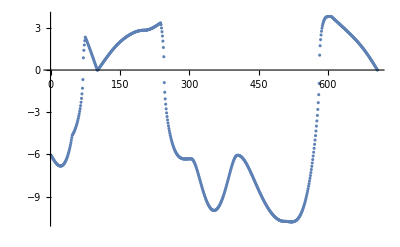

```mathematica
ListPlot@Table[originalBandi[i],{i,1,1}]
```

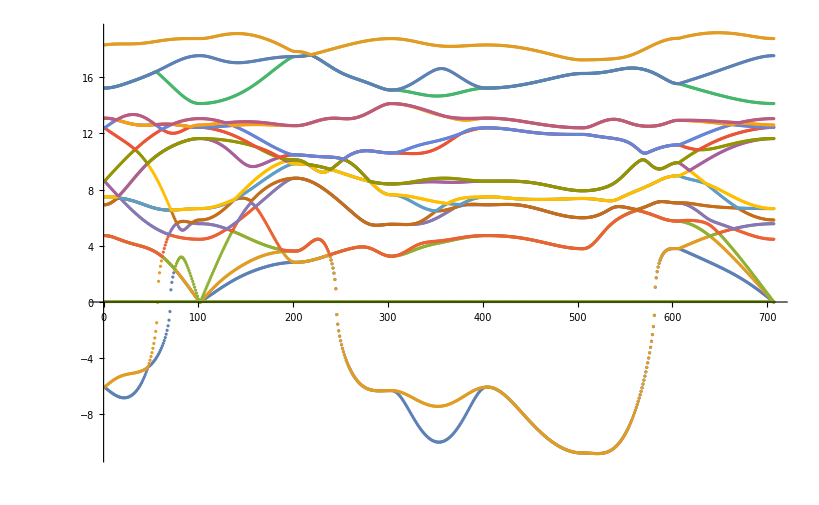

```mathematica
ListPlot@Table[originalBandi[i],{i,1,18}]
```